## Load data

```mathematica
SetDirectory@NotebookDirectory[];
data=Import["../_Data/supplementary_data.xlsx"];
docs=data[[3]]; (*COLUMN NAMES: {"id","original","place","Latitude","Longitude","year","month","other","vydavatel","vydavatel2"}*)
docs[[2;;All,5]]=Round@docs[[2;;All,5]]; (*round years*)
docList=docs[[2;;All,1]]; (* document names only *)
issuerList=Union[docs[[2;;All,-2]]];  (* issuer names only *)
yearList=Union[docs[[2;;All,5]]];
missing={#,0}&/@Complement[Range[yearList[[1]],yearList[[-1]]],yearList];
(* years without any documents *)
funcList=data[[6,2;;All]]; (* function names only *)

incid=data[[4]]/.""->0;
names=DeleteCases[Drop[incid[[All,2]],1],0];
incid=incid[[2;;Length@names+1,Flatten[Position[incid[[1]],#]&/@docList]]];(* Same ordering as in docs *)
incidFunc=incid;
incid=incid/._String->1;
incid=SparseArray[incid,{Length@names,Length@docList}];
```

### Functions

```mathematica
makeNet[minYear_,maxYear_]:=Module[{selectDoc,selectPos,adjNam,g},
selectDoc=Cases[docs,{x_,_,_,_,year_,_,_,_}:>x/;minYear≤year≤ maxYear];
selectPos=Flatten[Position[docList,#]&/@selectDoc];
adjNam=ArrayRules@SparseArray[incid[[All,selectPos]].Transpose[incid[[All,selectPos]]]-SparseArray@IdentityMatrix[Length[names]],Automatic,0]; (* make adjacency from incidence matrix *)
adjNam=DeleteCases[adjNam,PatternSequence[{x_,x_}->_]];
AppendTo[adjNam,{_,_}->∞];
g=WeightedAdjacencyGraph[SparseArray[adjNam,Length[names]]];
{adjNam,g}
];
```

```mathematica
makeFunc[minYear_,maxYear_]:=Module[{selectDoc,selectPos,adjNam,g},
selectDoc=Cases[docs,{x_,_,_,_,year_,_,_,_}:>x/;minYear≤year≤ maxYear];
selectPos=Flatten[Position[docList,#]&/@selectDoc];
incidFunc[[All,selectPos]]
];
```

```mathematica
Clear[calcRank];
(* alpha parameter used following: Opsahl et al. 2010 *)
calcRank[net_,type_,alpha_]:=calcRank[net,type,alpha]=Module[{d,s,vv,sg,ng,temp,maxRank,centrality,comps},
comps=ConnectedComponents[net[[2]]];
sg=Subgraph[net[[2]],comps[[1]]];
centrality=ConstantArray[0,VertexCount@net[[2]]];

Switch[type,
"d",d=VertexDegree[sg];s=Total@WeightedAdjacencyMatrix[sg];centrality[[VertexList[sg]]]=Switch[alpha,0,d,1,s,_,(If[#==0,0,#^(1-alpha)]&/@d)s^alpha];,
"e",{vv}=Eigenvectors[1.Normal@If[alpha==0,AdjacencyMatrix[sg],WeightedAdjacencyMatrix[sg]],1];
centrality[[VertexList[sg]]]=Normalize[Abs[vv],Total];,
"b"(* no weighted paths in this version *),ng=Graph[VertexList[net[[2]]],{Null,AdjacencyMatrix[net[[2]]]}];
ng=SetProperty[ng,EdgeWeight->PropertyValue[net[[2]],EdgeWeight]^-alpha];centrality=BetweennessCentrality[ng];,
"c",ng=Graph[VertexList[sg],{Null,AdjacencyMatrix[sg]}];
ng=SetProperty[ng,EdgeWeight->PropertyValue[sg,EdgeWeight]^-alpha];
centrality[[VertexList[sg]]]=ClosenessCentrality[ng];
];

temp=MapIndexed[({#1/.{x_,_?NumberQ}:>x,#2[[1]]-1})&,GatherBy[SortBy[Transpose[{Range[Length[names]],centrality}],Last],Last]];
maxRank=Max@Transpose[temp][[2]];
temp=Sort@Flatten[Transpose@{#[[1]],ConstantArray[#[[2]]/maxRank,Length[#[[1]]]]}&/@temp,1]
];
cent2rank[centrality_]:=Module[{temp,maxRank},
temp=MapIndexed[({#1/.{x_,_?NumberQ}:>x,#2[[1]]-1})&,GatherBy[SortBy[Transpose[{Range[Length[names]],centrality}],Last],Last]];
maxRank=Max@Transpose[temp][[2]];
temp=Sort@Flatten[Transpose@{#[[1]],ConstantArray[#[[2]]/maxRank,Length[#[[1]]]]}&/@temp,1];
temp[[All,2]]
];
```

### Make networks

```mathematica
wholeNet=makeNet[yearList[[1]],yearList[[-1]]];
nn=VertexCount[wholeNet[[2]]];
ee=EdgeCount[wholeNet[[2]]];
```

```mathematica
segments={1243,1248,1250,1252,1254,1257};
nets=Table[
makeNet[segments[[c]],segments[[c+1]]-1]
,{c,1,Length@segments-1}];
```

```mathematica
(*(* This one takes some time *)
nets=ParallelTable[makeNet[year,year],{year,yearList}];*)
```

### Graphics

```mathematica
Needs["PlotLegends`"];
colors={Directive[RGBColor[0.34398, 0.49112, 0.89936],Thick],Directive[RGBColor[0.97, 0.606, 0.081],(*Dashing[0.015],*)Thick](*Directive[Black,Thick]*),Directive[RGBColor[0.09096, 0.6296, 0.85532],Thick(*,DotDashed*)],Directive[RGBColor[0.448, 0.69232, 0.1538](*,Dashing[0.03]*),Thick],Directive[RGBColor[0.62168, 0.2798, 0.6914],Thick(*,Dashing[0.015]*)],Directive[RGBColor[0.8680706456216862, 0.2563858708756628, 0.30321559063052295],Thickness[0.02]]};
marker2=Graphics[{RGBColor[0.34398, 0.49112, 0.89936],Disk[{1/2,1/2}]},ImageSize->11];
marker3=Graphics[{EdgeForm[Directive[Thick,RGBColor[0.97, 0.606, 0.081],Opacity[1]]],White,Triangle[{{0,0},{1,0},{1/2,√3/2}}]},ImageSize->13];
marker4=Graphics[{RGBColor[0.09096, 0.6296, 0.85532],Disk[{1/2,1/2}]},ImageSize->markSize];
marker5=Graphics[{EdgeForm[Directive[Thick,RGBColor[0.448, 0.69232, 0.1538],Opacity[1]]],White,Disk[{1/2,1/2}]},ImageSize->11];
marker1=Graphics[{RGBColor[0.62168, 0.2798, 0.6914],Polygon[-1/2+2{{0,0},{0,1},{1,1},{1,0}}]},ImageSize->11];
marker6=Graphics[{RGBColor[0.8680706456216862, 0.2563858708756628, 0.30321559063052295],Thick,Line[{{.5,-1},{.5,2}}]},ImageSize->0.5markSize];
markers={marker2,marker3,marker4,marker5,marker1,marker6};
```

## Centrality and (ground truth) offices

### Prepare a dataset with ranks and centralities

```mathematica
(* Categorise office ranks *)
ranks=Join[Thread[funcList[[All,2]]->(funcList[[All,3]])],{0->"NA",1.->"witness"}];

(* Make a dataset with centralities *)
funcDS=Dataset@Table[
temp=makeFunc[segments[[c]],segments[[c+1]]-1]/.ranks;
base=<|"NA"->1,"witness"->1,"high"->1,"low"->1,"regional"->1,"issuer"->1,"mention"->1|>;
temp=Table[
temp1=Tally@Join[{"NA","witness","high","low","regional","issuer","mention"},temp[[i]]];
(Association[Thread[temp1[[All,1]]->temp1[[All,2]]]]-base),{i,1,Length@temp}];

Association[
ToString@segments[[c]]<>"-"<>ToString[segments[[c+1]]-1]->MapIndexed[AppendTo[temp[[#2[[1]]]],Append[Association@Thread[{"d0","c0","e0","d1","c1","e1","b1","d0.5","c0.5","d1.5","c1.5"}->#1],Association["name"->names[[#2[[1]]]]]]]&,
Transpose@Table[
1.calcRank[nets[[c]],i[[1]],i[[2]]][[All,2]]
,{i,{{"d",0(*degree*)},{"c",0(*unweighted closeness *)},{"e",0(*unweighted eigenvector*)},{"d",1(*strength*)},{"c",1(*inverse weighted*)},{"e",1(*weighted*)},{"b",1},{"d",0.5},{"c",0.5},{"d",1.5},{"c",1.5}}}]
]
]
,{c,1,5}];
```

```mathematica
Export["../_Data/funcDS.m",funcDS];
```

### Compute regression of centrality ranking versus manually categorised office ranks

```mathematica
Do[
temp=funcDS[c,1,Select[#witness+#high+#low+#regional+#issuer+#mention>0&],{"witness","high","low","regional","issuer",cent}];
nom=LinearModelFit[{Which["high">0,{0,1,0,0,0},"low">0,{0,0,1,0,0},"regional">0,{0,0,0,1,0},"witness">0,{1,0,0,0,0},"issuer">0,{0,0,0,0,1},True,{0,0,0,0,0}]/.#&/@Normal@temp,Normal@temp[All,cent]},{witness,high,low,regional,issuer},NominalVariables->{witness,high,low,regional,issuer}];
res[c,cent]=nom["ParameterConfidenceIntervalTableEntries"][[All,{1,2}]];
,{c,1,5},{cent,{"d0","c0","e0","b1","d1","c1","e1","d0.5","c0.5","d1.5","c1.5"}}];
```

### Plot results

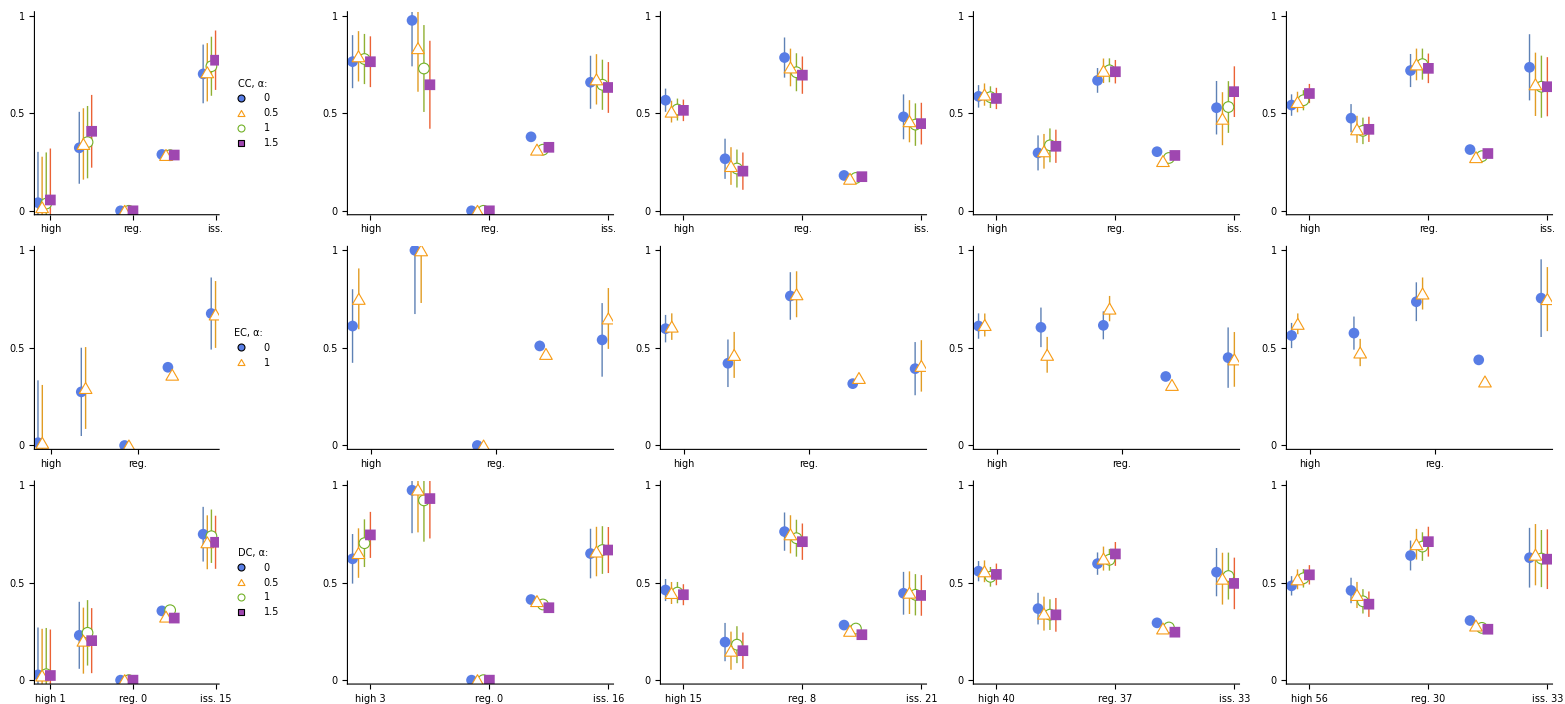

```mathematica
cent={{"c0","c0.5","c1","c1.5"},{"e0","e1"},{"d0","d0.5","d1","d1.5"}};
Grid@Table[
Table[
funcNo={"high","low","regional","witness","issuer"}/.Normal@funcDS[c,1,Select[#witness+#high+#low+#regional+#issuer+#mention>0&],{"witness","high","low","regional","issuer"}][Total];
Show[
ListPlot[
Table[MapIndexed[{#2[[1]]+i/10,Around@@#1}&,res[c,centlist[[i]]][[{2,3,4,1,5}]]]
,{i,1,Length@centlist}],PlotStyle->colors[[{1,2,4,5}]],PlotMarkers->markers[[{1,2,4,5}]],PlotLegends->If[c==1,Placed[PointLegend[(Style[""<>StringDrop[#,1],FontSize->14,FontFamily->"Helveticae",Black]&/@centlist),LegendLabel->Style[Switch[StringTake[centlist[[1]],1],"b","BC","d","DC","e","EC","c","CC"]<>", α:",FontSize->14,FontFamily->"Helveticae",Black,Bold]],{.6,.7}],None],PlotLabel->If[centlist=={"b0","b0.5","b1"},ToString@segments[[c]]<>"-"<>ToString[segments[[c+1]]-1],None]
]
,PlotRange->{Full,{0,1}},AxesStyle->Directive[FontSize->16,FontFamily->"Helveticae",Black],AxesLabel->If[centlist=={"b0","b0.5","b1"},{None,"rank"},None],LabelStyle->{FontFamily->"Helveticae",FontSize->18,Black},
Ticks->If[centlist=={"d0","d0.5","d1","d1.5"},{{{1.4,"high\n"<>ToString[funcNo[[1]]],{0.02,0}},{2.4,"low\n"<>ToString[funcNo[[2]]],{0.02,0}},{3.4,"reg.\n"<>ToString[funcNo[[3]]],{0.02,0}},{4.4,"wit.\n"<>ToString[funcNo[[4]]],{0.02,0}},{5.4,"iss.\n"<>ToString[funcNo[[5]]],{0.02,0}}},{0,.5,1}},{{{1.4,"high",{0.02,0}},{2.4,"low",{0.02,0}},{3.4,"reg.",{0.02,0}},{4.4,"wit.",{0.02,0}},{5.4,"iss.",{0.02,0}}},{0,.5,1}}],TicksStyle->Directive[FontSize->16,FontFamily->"Helveticae",Black],GridLines->None(*{{0},{0}}*),ImageSize->250,AspectRatio->1
],{c,1,5}]
,{centlist,cent}]
```